# UpSetChart Tests

```mathematica
Quit[];
```

```mathematica
$Path=Prepend[$Path,NotebookDirectory[]];
<<UpSetChart`
```

```mathematica
<<UpSetChart`TestData`
sets=DummyData[3]
```

<|Red→{Strawberry,Apple},Green→{Kiwi,Pear,Cucumber,Pickle},Tasty→{Kiwi,Pear},Fruit→{Kiwi,Lemon,Banana,Strawberry,Pear,Apple,Carrot},Vegetable→{Cucumber,Pickle}|>

<|a→{18,60,16,13,25,62,59,58,73,29},b→{69,61},c→{44,2,3,45,24},d→{3,8,19,93,14,1,81,40,90,96,82,87,45,43,98,86,65,4},e→{36,3,31,91,16,39,5,71},f→{79,43,41,77,90,5,3,27,24,74,80},g→{56,90,79,67,58,40,88,9,55,3,53,16,97,85,45,75,42,63},h→{45,1,80,23,61,90},i→{32,50,96,58,65,81,79,86,20,88,56,14,53,92,77,46},j→{93,46,52,100,11,48,25,26,31,12,90,10,39,64,87,95,86,79,49,69},k→{16,85,75,53,68,64,42,98,43,77,90,48,37,94,18,91,58,7,12,5,6},l→{65,95,26,15},m→{75,62,57,20,55,67,73,48,18,58,71,44,26,30,47,79,78,25},n→{51,34,50,81,84,15,100,96,61,12,68,74,59,87,41,62,47,75,26,60,44,89,66,24,58,40},o→{55,21,32,52,51,62,54,88,84,25,50,24,99,30,85,57,74,80,89},p→{54,78,61,82,43,8,12,38,22,89,35,18,3,65,92,15,1,55,66,16,72,24,67,84,87,44,69,49},q→{83,98,78,44,76},r→{27,95,44,40,25,76,77,64},s→{84,92,44,96,39},t→{13,3,53,62,99,93}|>

```mathematica
Sort@Keys@sets
```

{Fruit,Green,Red,Tasty,Vegetable}

```mathematica
DynamicUpSetChart[sets,"TabbedByComparisonsDegreeQ"->True,"ImageSize"->{Automatic,100}]
```

## The Packages of UpSetChart

```mathematica
2^20
```

1048576

```mathematica
Options[BarChart][[;;,1]]
```

{AlignmentPoint,AspectRatio,Axes,AxesLabel,AxesOrigin,AxesStyle,Background,BarOrigin,BarSpacing,BaselinePosition,BaseStyle,ChartBaseStyle,ChartElementFunction,ChartElements,ChartLabels,ChartLayout,ChartLegends,ChartStyle,ColorFunction,ColorFunctionScaling,ColorOutput,ContentSelectable,CoordinatesToolOptions,DisplayFunction,Epilog,FormatType,Frame,FrameLabel,FrameStyle,FrameTicks,FrameTicksStyle,GridLines,GridLinesStyle,ImageMargins,ImagePadding,ImageSize,ImageSizeRaw,Joined,LabelingFunction,LabelingSize,LabelStyle,LegendAppearance,Method,PerformanceGoal,PlotLabel,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PlotTheme,PreserveImageOptions,Prolog,RotateLabel,ScalingFunctions,TargetUnits,Ticks,TicksStyle}

```mathematica
d=RandomData[20];
```

```mathematica
p=UpSetChart[d,"DropEmpty"->True, "SetSortBy"->"Cardinality", "IntersectionSortBy"-> "Cardinality","TabbedByComparisonsDegreeQ"->True,"ImageSize"->{Automatic, 250}]
```

12345

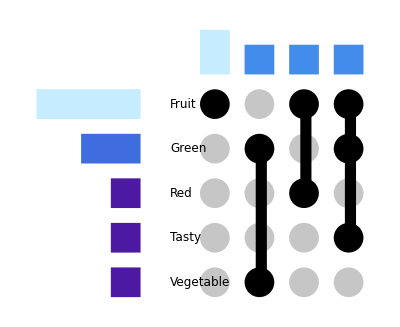

```mathematica
upc=UpSetChart[sets]
```

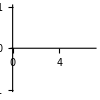
-Graphics-
-Graphics-

```mathematica
Graphics[
{
upc[[1]],
 Inset[
Graphics[{Opacity[0],Line[{{0,0},{7,0}}]},
Axes->{True, False},
ImageMargins->0,
ImagePadding->None,
ImageSize->{100,100},
AxesOrigin->{0,0}
(*,PlotRange->{{0,7},{0,3}}*)
(*,ImageSize->{7,100}*),
Ticks->{{{0,7}}}
],
{0,16},{0,0}
]
},
ImageMargins->0,
ImageSize->Automatic,
ImagePadding->None
]
```

```mathematica
EnsureLa
```

```mathematica
res=Table[
UpSetChart[sets, 
"DropEmpty"->dropEmpty, 
"SetSortBy"->setSort,
 "IntersectionSortBy"->compSort,
"TabbedByComparisonsDegreeQ"->False
], {dropEmpty, {True, False}}, {setSort, {"Name", "Cardinality"}}, {compSort, {"Name","Cardinality"}}
]
```

```mathematica
res2=Table[
UpSetChart[sets, 
"DropEmpty"->dropEmpty, 
"SetSortBy"->setSort,
 "IntersectionSortBy"->compSort,
"TabbedByComparisonsDegreeQ"->True,
"ImageSize"->{Automatic, 200}
], {dropEmpty, {True}}, {setSort, {"Name", "Cardinality"}}, {compSort, {"Name","Cardinality"}}
]
```

{{{123,123},{123,123}}}

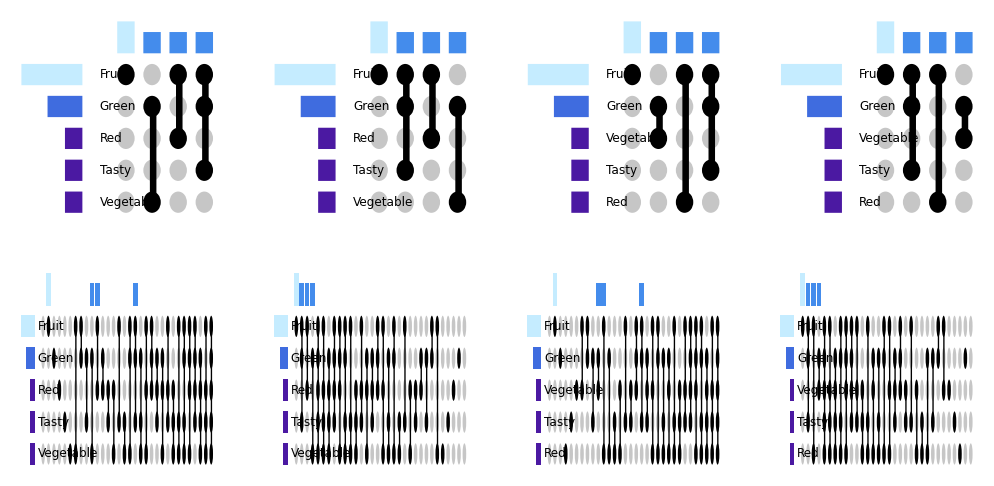

```mathematica
GraphicsGrid[Partition[Flatten[Join[res,res2]],{4}]]
```

```mathematica
UpSetChart[sets,"TabbedByComparisonsDegreeQ"->True ]
```

123

## Unique Intersections

```mathematica
(* Calculates the unique elements for the comparisons *)
<<UpSetChart`UniqueIntersections`
```

```mathematica
UniqueIntersections[<|"a"->{}|>]
```

<|sets→<|a→{}|>,setNames→{a},comparisons→{{},{a}},numberOfSets→1,elementsUniqueToComparisons→<|{}→{},{a}→{}|>|>

## Utilities

Utilities contains several conditional checkers and helpers.

```mathematica
(* Conditionals for types & passing down options *)
<<UpSetChart`Utilities`
```

```mathematica
EnsureLabeledSets[{{1,2,3},{2,3,4,4,4}}]
```

<|a→{1,2,3},b→{2,3,4}|>

```mathematica
EnsureLabeledSets[{{},{}}]
```

<|a→{},b→{}|>

```mathematica
sets={{1,2,3},{2,3,4,4,4}};
ListOfListsQ[sets]
LabeledSetsQ[sets]
LabeledSetsQ[EnsureLabeledSets[sets]]
```

True

False

True

## Calculations

While Unique Intersections does all the calculations we need for this chart, the chart may want us to sort and filter results as well.
This “super” function does this.

```mathematica
(* Calls UniqueIntersections and sorts & filters data *)
<<UpSetChart`Calculations`
```

```mathematica
calc=CalcThenSortAndFilter[sets]
```

<|sets→<|Vegetable→{Cucumber,Pickle},Tasty→{Kiwi,Pear},Red→{Strawberry,Apple},Green→{Kiwi,Pear,Cucumber,Pickle},Fruit→{Kiwi,Lemon,Banana,Strawberry,Pear,Apple,Carrot}|>,comparisons→<|{Fruit}→{Banana,Carrot,Lemon},{Green,Vegetable}→{Cucumber,Pickle},{Red,Fruit}→{Apple,Strawberry},{Green,Tasty,Fruit}→{Kiwi,Pear}|>|>

### Calculation Utilities

```mathematica
(* Sort & filter functions *)
<<UpSetChart`Calculations`Utilities`
```

## Graphics

```mathematica
(* Returns the graphics for UpSetChart *)
<<UpSetChart`Graphics`
```

Graphics is a wrapper GraphicComponents returning the Graphic Item. Allows for processing of the Options before passing them

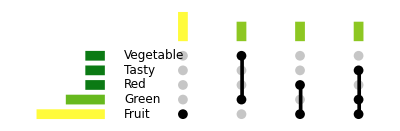

```mathematica
UpSetGraphics[
	calc["sets"], 
	calc["comparisons"],
	"ColorGradient"->"AvocadoColors",
	"ComponentSpacing"->{1,1},
	"IndicatorRadius"->0.5,
	"IndicatorSpacing"->{5,1/2}
]
```

### Utilities

Graphic Utilities is a wrapper over the four main components and returns them as a list.

```mathematica
(* Returns each components for the UpSetChart *)
<<UpSetChart`Graphics`Utilities`
```

```mathematica
gc=GraphicComponents[calc["sets"], calc["comparisons"],"IndicatorRadius"->1];
```

```mathematica
Show[
Graphics[{},
 Inset[
gc[[1]],
Axes->{True, False},
ImageMargins->0,
ImagePadding->None,
ImageSize->{100,100},
AxesOrigin->{0,0}
(*,ImageSize->{7,100}*)
]],
{0,16},{0,0}
],
Graphics[gc[[2]]],
Graphics[gc[[3]]],
Graphics[gc[[4]]]
]
```

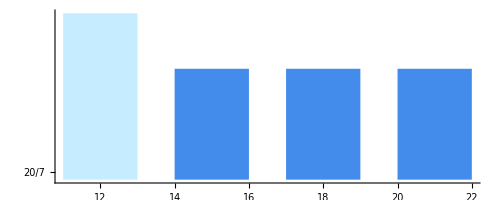

```mathematica
Graphics[{
Inset[
Graphics[
gc[[2]], 
Axes->{False,True},
Ticks->{Automatic, SetsBarChartsTicks[20, 8]}
]
]
}
]
```

```mathematica
maxValue=7;
nTicks=maxValue+1;
nTicks=5;
ticks=
Join[
{
{0, maxValue}
},

Table[
{maxValue/(nTicks-1)*i,maxValue-maxValue/(nTicks-1)*i},
{i,nTicks-1}
]]
```

{{0,7},{7/4,21/4},{7/2,7/2},{21/4,7/4},{7,0}}

```mathematica
ClearAll[NumberOfTicks]
Options[NumberOfTicks]={"ReversedQ"->False}
NumberOfTicks[maxValue_,numberOfTicks_,OptionsPattern[]]:=
With[
{
ReversedQ = OptionValue["ReversedQ"]
},
Join[
{
If[ReversedQ,{0, maxValue},{0, 0}]
},
With[
{
partition=maxValue/(numberOfTicks-1)
},
Table[
{
partition*i,
If[ReversedQ,
maxValue-partition*i,
partition*i
]
},
{i,numberOfTicks-1}
]]
]
]
```

{ReversedQ→False}

```mathematica
NumberOfTicks[7, 8]
```

{{7,0},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7}}

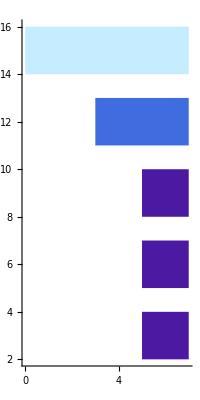

```mathematica
Graphics[{
Inset[Graphics[
gc[[1]], Axes->{True,False},
Ticks->{
NumberOfTicks[7, 8,"ReversedQ"->False],
Automatic
}
],{0,0}]
}
]
```

### Comparisons Bar Chart

Comparisons Bar Chart produces the bar chart for the cardinality of the set comparisons

```mathematica
(* Components for charts *)
<<UpSetChart`Graphics`ComparisonsBarChart`
```

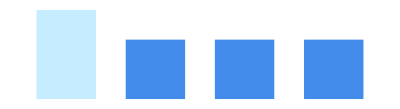

```mathematica
ComparisonsBarChart[calc["comparisons"],
 Max[Length/@calc["comparisons"]], Keys@calc["sets"]
]//Graphics[#,ImageSize->Tiny]&
```

### Grid Indicator

Grid Indicator produces the bubble heatmap which indicates which sets correspond to which comparisons

```mathematica
<<UpSetChart`Graphics`IndicatorGrid`
```

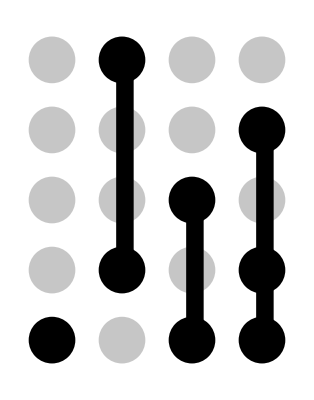

```mathematica
IndicatorGrid[Keys[calc["sets"]],Keys[calc["comparisons"]]]//Graphics[#,ImageSize->Tiny]&
```

### Sets Bar Chart

Produces the Bar Chart for the cardinality of sets

```mathematica
<<UpSetChart`Graphics`SetsBarChart`
```

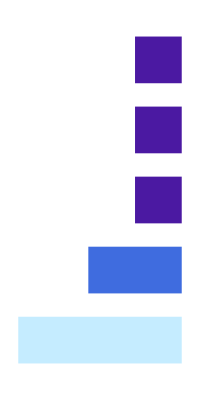

```mathematica
SetsBarChart[calc["sets"], Keys[calc["sets"]], Max[Length/@calc["sets"]]]//Graphics[#,ImageSize->Tiny]&
```

### Labels

Produces the labels of the sets. Works best with short labels

```mathematica
<<UpSetChart`Graphics`SetsLabels`
```

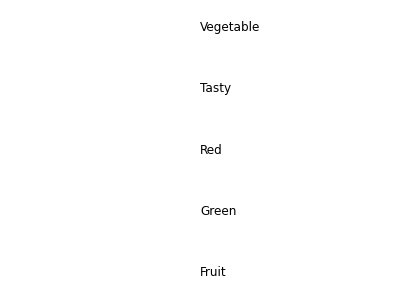

```mathematica
SetsLabels[ Keys[calc["sets"]]]//Graphics[#,ImageSize->Tiny]&
```